# Supplementary Material for Modeling Food Dependent Symbiosis in Exaiptasia pallida

## Authors: Jakob O. Kaare-Rasmussen, Holly V. Moeller, and Ferdinand Pfab

## Nutrient Limitations of Symbiont and Host

Supplementary Material Figure S2

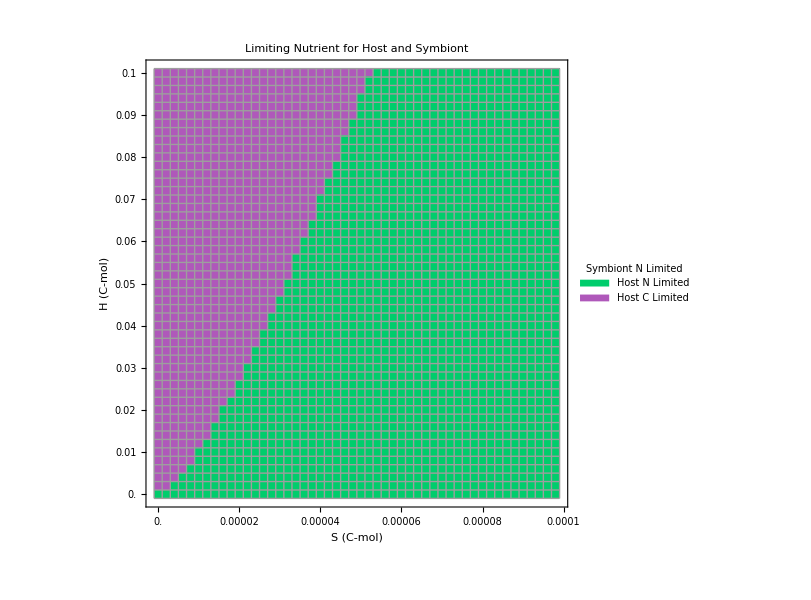

```mathematica
ClearAll["Global`*"]
colors={h->ColorData[97][2],s->ColorData[97][1]}; 
red=ResourceFunction["HexToColor"]["#FF1F5b"];
green=ResourceFunction["HexToColor"]["#00CD6C"];
blue = ResourceFunction["HexToColor"]["#009ADE"];
purple=ResourceFunction["HexToColor"]["#AF58BA"];
yellow=ResourceFunction["HexToColor"]["#FFC61E"];
orange=ResourceFunction["HexToColor"]["F28522"];
bestfit={aX->0.07243165880437435,wX->0.0026142991079086157,pX->27.700459925037663,ynX->0.060192963245436854,dsX->0.7709975010970849,dhX->0.12619563820188512,h0X->6.502940605096842*^-6,s0X->1.0227841615913929*^-10,rcX->0.009992087726261166,rnX->0.014645292219590888};(*paraeter fits in X format*)
fipar={a->0.07243165880437435,w->0.0026142991079086157,p->27.700459925037663,yn->0.060192963245436854,ds->0.7709975010970849,dh->0.12619563820188512,rc->0.009992087726261166,rn->0.014645292219590888};(*parameter fits without X format*)
parsFixed={nnh->0.18,nns->0.13};(*fixed parameter alues*)
tmax=8; (* 8-week time set *)
sim[pars_]:=Module[{jsc,jsn,jhc,jhn,jsg,jst,jhg,jht,f},(*Simulation*)
f=s[t](a h[t])/(s[t]+a w h[t]);(*equation 13*)
jsc=p s[t]; (*equation 6*)
jsn=yn nnh f; (*equation 5*)
jhc= p s[t]-Min[jsc,nns^-1 jsn]+rc h[t]^(2/3);(*equations 10 and 11*)
jhn=rn  h[t]^(2/3);(*equation 9*)
jsg=Min[jsc,nns^-1 jsn]; (*equation 3*)
jst=ds s[t]; (*equation 4*)
jhg=Min[jhc,nnh^-1 jhn];(*equation 7*)
jht=dh h[t] + f;(*equation 8*)
Quiet@NDSolve[
{
s'[t]==jsg-jst,(*equation 1*)
h'[t]==jhg-jht,(*equation 2*)
s[0]==s0,
h[0]==h0
}/.pars,
{s,h},
{t,0,tmax},Method->{Automatic,"DiscontinuityProcessing"->None},WorkingPrecision->20][[1]]];
pars[treatment_]:=(*parameter choices function*)Piecewise[{{Join[{a->aX,w->wX,p->pX,yn->ynX,ds->dsX,dh->dhX,rc->0,rn->0,s0->0,h0->h0X},parsFixed], treatment=="as"}, {Join[{a->aX,w->wX,p->pX,yn->ynX,ds->dsX,dh->dhX,rc->rcX,rn->rnX,s0->0,h0->h0X},parsFixed], treatment=="af"}, {Join[{a->aX,w->wX,p->pX,yn->ynX,ds->dsX,dh->dhX,rc->rcX,rn->rnX,s0->s0X,h0->h0X},parsFixed], treatment=="if"}, {Join[{a->aX,w->wX,p->pX,yn->ynX,ds->dsX,dh->dhX,rc->0,rn->0,s0->s0X,h0->h0X},parsFixed], treatment=="is"}}]
(*Function that calculates limiting nutrients given an S and H*)
lim[x_,y_]:=Module[{jsc,jsn,jhc,jhn,jsg,jst,jhg,jht,f,ic},
ic={h0->y,s0->x};
f=s0(a h0)/(s0+a w h0);(*equation 13*)
jsc=p s0; (*equation 6*)
jsn=yn nnh f; (*equation 5*)
jhc= p s0-Min[jsc,nns^-1 jsn]+rc h0^(2/3);(*equations 10 and 11*)
jhn=rn  h0^(2/3);(*equation 9*)
jsg=Min[jsc,nns^-1 jsn]; (*equation 3*)
jst=ds s0; (*equation 4*)
jhg=Min[jhc,nnh^-1 jhn];(*equation 7*)
jht=dh h0 + f;(*equation 8*)
If[(jsc>jsn∧jhc>jhn)/.fipar/.ic/.parsFixed,1(*Print["SNHN"]*),
If[(jsc>jsn∧jhc<jhn)/.fipar/.ic/.parsFixed,2(*Print["SNHC"]*),
If[(jsc<jsn∧jhc<jhn)/.fipar/.ic/.parsFixed,3(*Print["SCHC"]*),4(*Print["SCHN"]*)]]]]
out2=Table[
Table[
lim[s,h],{s,10^-15,.0001,.000002}],{h,0,0.1,.002}];(*calculate nutrint liitation given an S and H*)
plotout2=ArrayPlot[Reverse[out2],AspectRatio->1,ColorRules->{1->green,2->purple,3->Green,4->Blue},Mesh->True,PlotLegends->SwatchLegend[{"Host N Limited","Host C Limited",SCHC,SCHN},LegendLabel->"Symbiont N Limited"],Frame->True,FrameLabel->{"H (C-mol)","S (C-mol)"},FrameTicks->{{Table[{51-(h)/2,h.001},{h,0,100,10}],None},{Table[{(s/2+1),.000001s},{s,0,100,20}],None}},LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->20},ImageSize->600,PlotLabel->"Limiting Nutrient for Host and Symbiont"] (*plot Limiting nutrient*)
```

```mathematica
Export[NotebookDirectory[]<>"lims.jpg",plotout2]
```

/Users/JakobK-R/Desktop/lims.jpg

## Nutrient Limitation regimes when parameters are individually adjusted

Supplementary Materials Figure S3

```mathematica
jch[t_]:=h[t]^(2/3) rc+p s[t]-Min[p s[t],(a h[t] nnh s[t] yn)/(nns (s[t]+a h[t] w))](*host carbon*)
jnh[t_]:=h[t]^(2/3) rn(*host nitrogen*)
jcs[t_]:=p s[t](*symbiont carbon*)
jns[t_]:=(a h[t] nnh s[t] yn)/(s[t]+a h[t] w)(*symbiont nitrogen*)
(*Host: with symbiont, fed*)
dhoutif[varx_,var_,val_]:=Module[{sol},
sol=sim[pars["if"]/.varx->val/.bestfit]/.parsFixed;
(NIntegrate[jch[t]/.var->val/.sol/.parsFixed/.fipar,{t,0,8}]/(nnh NIntegrate[jnh[t]/.var->val/.sol/.parsFixed/.fipar,{t,0,8}]))/.parsFixed]
(*Host: without symbiont, fed*)
dhoutaf[varx_,var_,val_]:=Module[{sol},
sol=sim[pars["af"]/.varx->val/.bestfit]/.parsFixed;
(NIntegrate[jch[t]/.var->val/.sol/.parsFixed/.fipar,{t,0,8}]/(nnh NIntegrate[jnh[t]/.var->val/.sol/.parsFixed/.fipar,{t,0,8}]))/.parsFixed]
(*Symbiont: withsymbiont, fed*)
dsoutif[varx_,var_,val_]:=Module[{sol},
sol=sim[pars["if"]/.varx->val/.bestfit]/.parsFixed;
(NIntegrate[jcs[t]/.var->val/.sol/.parsFixed/.fipar,{t,0,8}]/(nns NIntegrate[jns[t]/.var->val/.sol/.parsFixed/.fipar,{t,0,8}]))/.parsFixed]
plotter[varx_,var_,rangea_,rangeb_,xlab_]:=
GraphicsRow[{
LogPlot[
{dsoutif[varx,var,x],1},
{x,rangea,rangeb},
PlotStyle->{{s/.colors},{Black,Dashed}},
Frame->True,
FrameLabel->{{Rotate[Style["(∫C)/(∫N)",FontSize->15],3π/2],None},{Style[xlab,FontSize->15],None}},
LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->10},ImageSize->1000,RotateLabel->True],
LogPlot[{dhoutif[varx,var,x],
dhoutaf[varx,var,x],1},
{x,rangea,rangeb},
PlotStyle->{{h/.colors},{h/.colors,Dashed},{Black,Dashed}},
LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->10},
Frame->True,
FrameLabel->{{Rotate[Style["(∫C)/(∫N)",FontSize->15],3π/2],None},{Style[xlab,FontSize->15],None}},ImageSize->1000]}]
w2=plotter[wX,w,0,0.1,w];
a2=plotter[aX,a,0,5,a];
p2=plotter[pX,p,0,40,p];
yn2=plotter[ynX,yn,0,0.06,Subscript[y,n]];
ds2=plotter[dsX,ds,0,5,Subscript[d,s]];
dh2=plotter[dhX,dh,0,3,Subscript[d,h]];
rc2=plotter[rcX,rc,0,0.1,Subscript[r,c]];
rn2=plotter[rnX,rn,0,0.005,Subscript[r,n]];
leg=LineLegend[{h/.colors,{h/.colors,Dashed},s/.colors,{Black, Dashed}},{"Host With Symbionts","Host Without Symbionts","Symbiont","(∫C)/(∫N)=1"},LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->15}]:
```

```mathematica
fulllim=GraphicsColumn[{leg,a2,w2,p2,yn2,ds2,dh2,rc2,rn2},ImageSize->1000]
```

-Graphics-

```mathematica
.
```

```mathematica
Export[NotebookDirectory[]<>"fulllim.jpg",fulllim]
```

/Users/JakobK-R/Desktop/fulllim.jpg

```mathematica
fulllima=GraphicsColumn[{leg,a2,w2,p2,yn2},ImageSize->1000]
fulllimb=GraphicsColumn[{ds2,dh2,rc2,rn2},ImageSize->1000]
```

```mathematica
Export[NotebookDirectory[]<>"fulllima.jpg",fulllima]
Export[NotebookDirectory[]<>"fulllimb.jpg",fulllimb]
```

/Users/JakobK-R/Desktop/fulllima.jpg

/Users/JakobK-R/Desktop/fulllimb.jpg

Supplementary Material Figure S4, S5 and S6

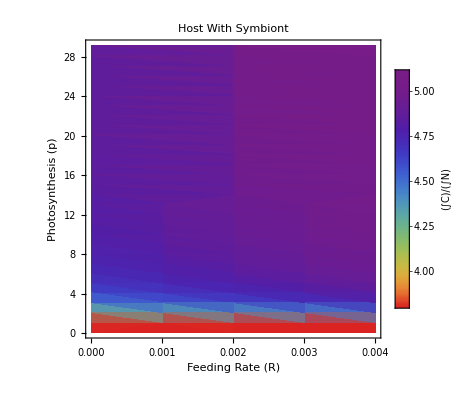

```mathematica
(*adjust functions with only r and p as inputs*)
γ=bestfit[[10,2]]/bestfit[[9,2]];
dhoutif2[r_,p_]:=Module[{sol},
sol=sim[pars["if"]/.{rcX->r,rnX->γ r}/.pX->p/.bestfit]/.parsFixed;
(NIntegrate[jch[t]/.{rcX->r,rnX->γ r}/.pX->p/.sol/.parsFixed/.fipar,{t,0,8}]/(nnh NIntegrate[jnh[t]/.{rcX->r,rnX->γ r}/.pX->p/.sol/.parsFixed/.fipar,{t,0,8}]))/.parsFixed]
(*Host: without symbiont, fed*)
dhoutaf2[r_,p_]:=Module[{sol},
sol=sim[pars["af"]/.{rcX->r,rnX->γ r}/.pX->p/.bestfit]/.parsFixed;
(NIntegrate[jch[t]/.{rcX->r,rnX->γ r}/.pX->p/.sol/.parsFixed/.fipar,{t,0,8}]/(nnh NIntegrate[jnh[t]/.{rcX->r,rnX->γ r}/.pX->p/.sol/.parsFixed/.fipar,{t,0,8}]))/.parsFixed]
(*Symbiont: withsymbiont, fed*)
dsoutif2[r_,p_]:=Module[{sol},
sol=sim[pars["if"]/.{rcX->r,rnX->γ r}/.pX->p/.bestfit]/.parsFixed;
(NIntegrate[jcs[t]/.{rcX->r,rnX->γ r}/.pX->p/.sol/.parsFixed/.fipar,{t,0,8}]/(nns NIntegrate[jns[t]/.{rcX->r,rnX->γ r}/.pX->p/.sol/.parsFixed/.fipar,{t,0,8}]))/.parsFixed]
out1=Flatten[Table[
Table[
{r,p,dhoutif2[r,p]},{r,0,0.0045,0.001}],{p,0.1,30,1}],1];
test1=ListDensityPlot[
out1,
PlotRange->Full,
ColorFunction->(ColorData["Rainbow",(1-#)^2]&),
FrameLabel->{"Feeding Rate (R)","Photosynthesis (p)"},
LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->15},
PlotLabel->"Host With Symbiont",
PlotLegends->BarLegend[Automatic,LegendLabel->Style["(∫C)/(∫N)",FontFamily->"Times New Roman",FontColor->Black,FontSize-> 20]]]
```

```mathematica
Export[NotebookDirectory[]<>"HWS.jpg",test1]
```

/Users/JakobK-R/Desktop/HWS.jpg

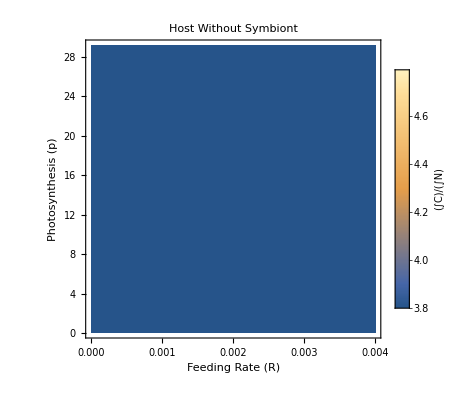

```mathematica
out3=Flatten[Table[
Table[
{r,p,dhoutaf2[r,p]},{r,0,0.0045,0.001}],{p,0.1,30,1}],1];

test3=ListDensityPlot[
out3,
PlotRange->All,
FrameLabel->{"Feeding Rate (R)","Photosynthesis (p)"},
LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->15}, 
 PlotLabel->"Host Without Symbiont",
PlotLegends->BarLegend[Automatic,LegendLabel->Style["(∫C)/(∫N)",FontFamily->"Times New Roman",FontColor->Black,FontSize-> 20]]]
```

```mathematica
Export[NotebookDirectory[]<>"HWOS.jpg",test2]
```

/Users/JakobK-R/Desktop/HWOS.jpg

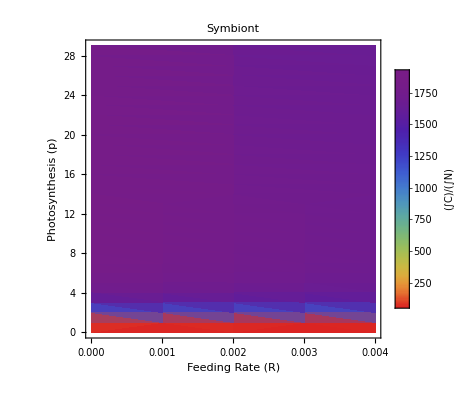

```mathematica
out2=Flatten[Table[
Table[
{r,p,dsoutif2[r,p]},{r,0,0.0045,0.001}],{p,0.0000000001,30,1}],1];
test2=ListDensityPlot[out2,PlotRange->All,ColorFunction->(ColorData["Rainbow",(1-#)^2]&),PlotLabel->"Symbiont",
LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->15},
FrameLabel->{"Feeding Rate (R)","Photosynthesis (p)"},
PlotLegends->BarLegend[Automatic,LegendLabel->Style["(∫C)/(∫N)",FontFamily->"Times New Roman",FontColor->Black,FontSize-> 20]]]
```

```mathematica
Export[NotebookDirectory[]<>"S.jpg",test3]
```

/Users/JakobK-R/Desktop/S.jpg

## Symbiont - Host phase plane

Supplementary Material Figure S1

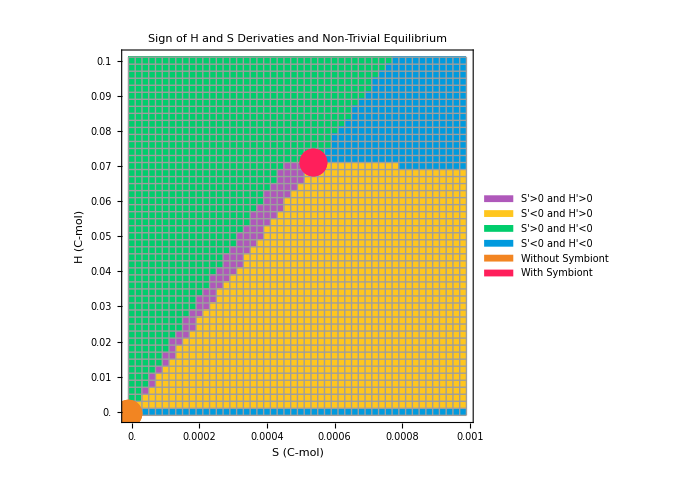

```mathematica
ClearAll["Global`*"]
red=ResourceFunction["HexToColor"]["#FF1F5b"];
green=ResourceFunction["HexToColor"]["#00CD6C"];
blue = ResourceFunction["HexToColor"]["#009ADE"];
purple=ResourceFunction["HexToColor"]["#AF58BA"];
yellow=ResourceFunction["HexToColor"]["#FFC61E"];
orange=ResourceFunction["HexToColor"]["F28522"];
fipar={a->0.07243165880437435,w->0.0026142991079086157,p->27.700459925037663,yn->0.060192963245436854,ds->0.7709975010970849,dh->0.12619563820188512,rc->0.009992087726261166,rn->0.014645292219590888};
parsFixed={nnh->0.18,nns->0.13};
lim2[x_,y_]:=Module[{jsc,jsn,jhc,jhn,jsg,jst,jhg,jht,f,ic,dhdt,dsdt},
ic={h0->y,s0->x};
f=s0(a h0)/(s0+a w h0);(*equation 13*)
jsc=p s0; (*equation 6*)
jsn=yn nnh f; (*equation 5*)
jhc= p s0-Min[jsc,nns^-1 jsn]+rc h0^(2/3);(*equations 10 and 11*)
jhn=rn  h0^(2/3);(*equation 9*)
jsg=Min[jsc,nns^-1 jsn]; (*equation 3*)
jst=ds s0; (*equation 4*)
jhg=Min[jhc,nnh^-1 jhn];(*equation 7*)
jht=dh h0 + f;(*equation 8*)
dhdt=jhg-jht;
dsdt=jsg-jst;
If[(dhdt>0∧dsdt>0)/.fipar/.ic/.parsFixed,1(*Print["SgHg"]*),
If[(dhdt>0∧dsdt<0)/.fipar/.ic/.parsFixed,2(*Print["SlHg"]*),
If[(dhdt<0∧dsdt>0)/.fipar/.ic/.parsFixed,3(*Print["SgHl"]*),4(*Print["SlHl"]*)]]]]
out3=Table[
Table[lim2[s,h],{s,10^-15,.001,.00002}],{h,0,0.1,.002}];(*calculate a large number of S and H combinations*)plotout=ArrayPlot[Reverse[out3],AspectRatio->1,ColorRules->{1->purple,2->yellow,3->green,4->blue},Mesh->True,PlotLegends->SwatchLegend[{"S'>0 and H'>0","S'<0 and H'>0","S'>0 and H'<0","S'<0 and H'<0"},LegendLabel->"Sign of Derivatives"],Frame->True,FrameLabel->{"H (C-mol)","S (C-mol)"},FrameTicks->{Reverse[Table[{51-h/2,0.001h},{h,0,100,10}]],Table[{s/2+1,s 0.00001},{s,0,100,20}]},PlotRange->Full,LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->15},ImageSize->600];(*plot S and H comination with corrispondint rates of change*)
eq1= {0,0.0004964044681961489};(*equilibrium*)
eq1o={0,500 0.0004964044681961489};(*equilibrium adjusted for plot*)
eq2={0.000539286,0.0705831};(*equilibrium*)
eq2o={50750 0.000539286,510 0.0705831};(*equilibrium adjusted for plot*)
plotoutnew=Show[plotout,
ListPlot[{{eq1o},{eq2o}},PlotStyle->{{orange,PointSize[.04]},{red,PointSize[.04]}},PlotLegends->SwatchLegend[{"Without Symbiont","With Symbiont"},LegendLabel->"Non-Trivial Equilibrium",LegendMarkers->"Bubble"],LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->15}],PlotLabel->Style["Sign of H and S Derivaties and Non-Trivial Equilibrium",FontSize->20],ImageSize->500](*add equalibrium to plot*)
```

```mathematica
Export[NotebookDirectory[]<>"phaseplane.jpg",plotoutnew]
```

/Users/JakobK-R/Desktop/phaseplane.jpg